```mathematica
FourierTransform[v^□,v,u]
```

FourierTransform[ⅇ^(-p^(-v z)),v,u]

```mathematica
Integrate[ⅇ^(2π ⅈ x)Abs[x]^s,{x,-∞,∞}]
```

Piecewise[{{ⅈ ⅇ^(-1/2 ⅈ π s) (-1+ⅇ^(ⅈ π s)) (2 π)^(-1-s) Gamma[1+s], -1<Re[s]<0}, {Integrate[ⅇ^(2 ⅈ π x) Abs[x]^s,{x,-∞,∞},Assumptions→Re[s]≥0||Re[s]≤-1], True}}]

```mathematica
1/(z Log[p])Gamma[(2π ⅈ u)/(z Log[p])+1/z-1]
```

Gamma[-1+1/z+(2 ⅈ π u)/(z Log[p])]/(z Log[p])

```mathematica
Integrate[1/(z Log[p])Gamma[(2π ⅈ u)/(z Log[p])+1/z-1] ⅇ^(2π ⅈ u v)/.{p->2,z->1/2},{u,-∞,∞}]
```

∫_(-∞)^∞ (ⅇ^(2 ⅈ π u v) Gamma[-1+1/z+(2 ⅈ π u)/(z Log[p])])/(z Log[p])ⅆu

```mathematica
1/(z Log[p])Gamma[(2π ⅈ u)/(z Log[p])+1/z-1]/.{p->2,z->1/2,u->1.}
```

-1.07135×10^-11-7.72263×10^-12 ⅈ

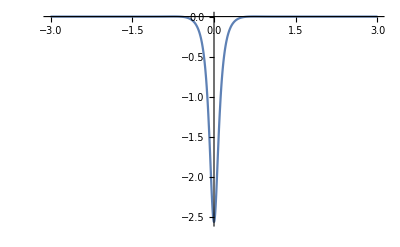

```mathematica
Plot[Re[1/(z Log[p])Gamma[(2π ⅈ u)/(z Log[p])+1/z-1]/.{p->2,z->2}],{u,-3,3},PlotRange->All]
```

```mathematica
Gamma[1.+10ⅈ]
```

3.91893×10^-7+1.12845×10^-6 ⅈ

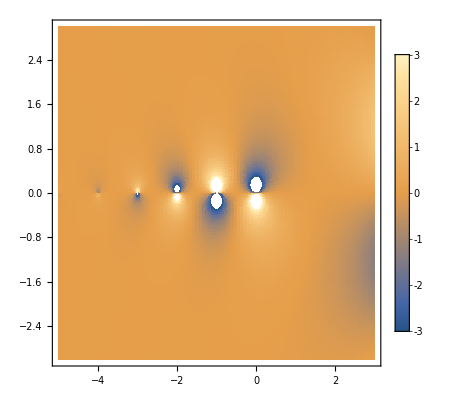

```mathematica
DensityPlot[Im[Gamma[x+ⅈ y]],{x,-5,3},{y,-3,3},PlotPoints->100,PlotRange->{-3,3},PlotLegends->Automatic]
```

```mathematica
Plot3D[Abs[Gamma[x+ⅈ y]],{x,-5,3},{y,-3,3},PlotPoints->100,PlotRange->{-5,5},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Gamma[x+ⅈ y]/.{x->-0.26,y->0.77}
```

-0.669092-0.52411 ⅈ

```mathematica
Integrate[Gamma[2π ⅈ u+1] ⅇ^(2π ⅈ u v)/.{p->2,z->1/2},{u,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(2 ⅈ π u v) Gamma[1+2 ⅈ π u]ⅆu

```mathematica
Series[ⅇ^(ⅈ t x),{x,0,6}]
```

1+ⅈ t x-(t^2 x^2)/2-1/6 ⅈ t^3 x^3+(t^4 x^4)/24+1/120 ⅈ t^5 x^5-(t^6 x^6)/720+O[x]^7

```mathematica
Series[ⅇ^(-x-ⅇ^-x),{x,0,6}]
```

1/ⅇ-x^2/(2 ⅇ)+x^3/(6 ⅇ)+x^4/(12 ⅇ)-(3 x^5)/(40 ⅇ)+x^6/(80 ⅇ)+O[x]^7

```mathematica
NIntegrate[1/π Gamma[1.+ⅈ t] t^4,{t,0,∞}]ⅇ
```

2.+3.12053 ⅈ

```mathematica
Integrate[ⅇ^-θ θ^(2π ⅈ k),{θ,0,∞}]
```

ConditionalExpression[Gamma[1+2 ⅈ k π],2 π Im[k]<1]

```mathematica
Integrate[ⅇ^(-θ^(z Log[p]))θ^((1-z)Log[p]+2π ⅈ k-1),{θ,0,∞}]
```

ConditionalExpression[Gamma[-1+1/z+(2 ⅈ k π)/(z Log[p])]/(z Log[p]),Re[Log[p]-z Log[p]]>2 π Im[k]&&Re[z Log[p]]>0]

```mathematica
NIntegrate[ⅇ^(-θ^(2 Log[2])) θ^(-1-Log[2]),{θ,0.1,1}]
```

4.72224

```mathematica
ⅇ^(-θ^(z Log[p]))θ^((1-z)Log[p]+2π ⅈ k-1)/.{z->2,p->2,k->0}
```

ⅇ^(-θ^(2 Log[2])) θ^(-1-Log[2])